```mathematica
θ=0.58;
V[x1_,x2_,d_,θ_]:=1/d-1/(√(d^2+2d Cos[θ]x1+x1^2))-1/(√(d^2-2d Cos[θ]x2+x2^2))+1/(√(d^2-2d Cos[θ](x2-x1)+(x2-x1)^2))+1/2 x1^2+1/2 x2^2
v[x_,d_,θ_]:=V[x,-x,d,θ]
$Post=Chop[#,10^-7]&;
energ=Module[{d,eqs,s,min,minPot,energies},
energies={};
Do[
d=i/100;
eqs={Together[D[v[x,d,θ],{x,1}]]//Numerator}//FullSimplify;
s=NSolve[eqs,{x},Reals];
min=Sort[s,(v[x,d,θ]/.#1)<=(v[x,d,θ]/.#2) &][[1]];
minPot=v[x,d,θ]/.min;
AppendTo[energies,{d,minPot}];
,{i,1.3*100,1.4*100}];
energies
];
```

```mathematica
V[-x,x,d,theta]//FullSimplify//FortranForm
```

1/d + x**2 + 1/Sqrt(d**2 + 4*x**2 - 4*d*x*Cos(theta)) - 2/Sqrt(d**2 + x**2 - 2*d*x*Cos(theta))

```mathematica
energ
```

{{1.3,-0.160062},{1.31,-0.137595},{1.32,-0.115365},{1.33,-0.0933731},{1.34,-0.0716194},{1.35,-0.0501049},{1.36,-0.0288306},{1.37,-0.00779746},{1.38,0},{1.39,0},{1.4,0}}

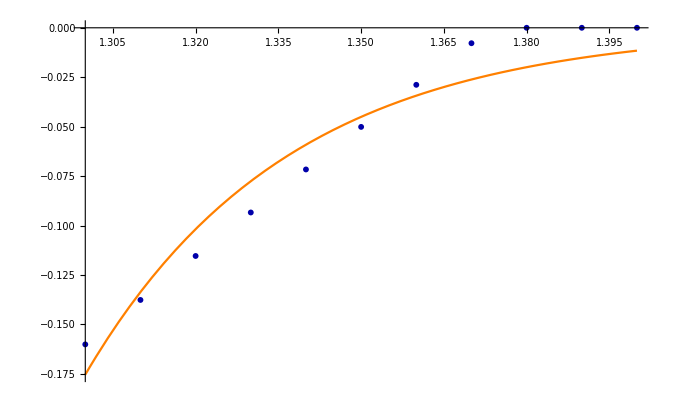

```mathematica
f[x_]:=Normal[NonlinearModelFit[energ[[;;]],-De Exp[-a r],{De,a},r,MaxIterations->∞]]/.r->x
Show[Plot[f[x],{x,1.3,1.4},PlotStyle->{Orange}],ListPlot[energ,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

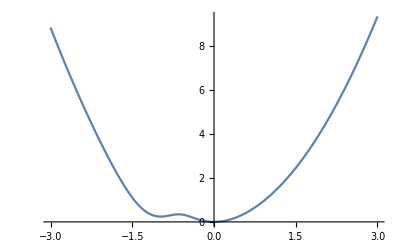

```mathematica
Plot[v[x,1.5,0.58],{x,-3,3}]
```

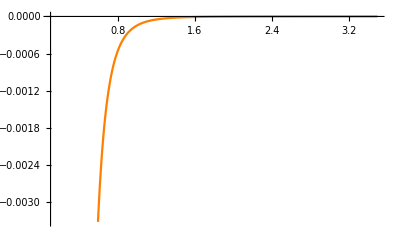

```mathematica
f[x_]:=Normal[NonlinearModelFit[energ,a/r^6+b/r^12,{a,b},r,MaxIterations->∞]]/.r->x
Show[Plot[f[x],{x,0.1,3.5},PlotStyle->{Orange}],ListPlot[energ,PlotMarkers->{Automatic,6},PlotStyle->Darker[Blue]]]
```

```mathematica
{Together[D[V[x1,x2,d,θ],{x1,1}]]//Together//Numerator,Together[D[V[x1,x2,d,θ],{x2,1}]]//Together//Numerator}//FullSimplify
```

{-0.836463 (1. d (d^2+1.67293 d x1+x1^2)^(3/2)+1.19551 x1 (d^2+1.67293 d x1+x1^2)^(3/2)-1. d (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 x1 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 x1 (d^2+1.67293 d x1+x1^2)^(3/2) (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)-1.19551 (d^2+1.67293 d x1+x1^2)^(3/2) x2),0.836463 (-1. d (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2)+1.19551 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2) x2+1. d (d^2-1.67293 d x2+x2^2)^(3/2)+1.19551 x1 (d^2-1.67293 d x2+x2^2)^(3/2)-1.19551 x2 (d^2-1.67293 d x2+x2^2)^(3/2)+1.19551 (d^2+(x1-x2)^2+1.67293 d (x1-1. x2))^(3/2) x2 (d^2-1.67293 d x2+x2^2)^(3/2))}

```mathematica
D[V[x1,x2,d,θ],{x1,1}]//Together//Numerator
```

-0.836463 d (d^2+1.67293 d x1+x1^2)^(3/2)-1. x1 (d^2+1.67293 d x1+x1^2)^(3/2)+(d^2+1.67293 d x1+x1^2)^(3/2) x2+0.836463 d (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)+x1 (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)+x1 (d^2+1.67293 d x1+x1^2)^(3/2) (d^2-1.67293 d (-x1+x2)+(-x1+x2)^2)^(3/2)